## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-uni/algebra/packages"],BaseDir="~/home-uni",BaseDir="~/uni"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;
Clear[SaveFigures];

KPImport[file_String,opts___]:=Module[{},
If[AbsoluteTime[FileDate[file]]<AbsoluteTime[{2013,3,7}],
Print[Style["Warning: File "<>file<>" is older than March 7, 2012!",FontColor->Red]];
];
Return[Import[file,opts]];
];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## Fit to oscillation + decay scenario

### Δm_41^2 vs. U_e4^2 vs. U_μ4^2

```mathematica
Clear[DataFiles];
ExpList={"lsnd-ivan","karmen-ivan","mbjk","opera","icarus","e776","betadecay","freestreaming","all","nolsnd","nocosmo"};

(* data files for intermediate-Subscript[m, 4] window *)
Suffix=".dat.gz";
M4GList={"0.1","0.2","1","10"};
MAM4List={"0.5","0.9"};
RunList=Flatten[Outer[List,ExpList,M4GList,MAM4List],2];
(*RunList=Append[RunList,{"app-proj"}];*)
For[i=1,i≤Length[RunList],i++,
If[Length[RunList⟦i⟧]>1, (* slices through parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>"-m4G"<>RunList⟦i,2⟧<>"-MAM4"<>RunList⟦i,3⟧<>Suffix,
(* Else - projections over parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>Suffix;
];
DataFilesBFP[i]="8-oscdecay/bfp-"<>RunList⟦i,1⟧<>Suffix;
If[FileExistsQ[StringReplace[DataFiles[i],Suffix->"-hires"<>Suffix]],
DataFiles[i]=StringReplace[DataFiles[i],Suffix->"-hires"<>Suffix];
];
];

Clear[mAm4,m4Γ,thisChi2Min,globalChi2Min,thisBFP,globalBFP,DataInterpol,DataReducedInterpol];
AllData=ParallelTable[Import[DataFiles[i],"Text"],{i,1,Length[RunList]}];
For[i=1,i≤Length[AllData],i++,
key=RunList⟦i⟧;
WriteString["stdout","Reading sample "<>ToString[key]<>" from "<>DataFiles[i]<>" ..."];
DataRaw[i]=AllData⟦i⟧;
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,Min[#⟦-2⟧,#⟦-1⟧]}&/@Cases[ImportString[DataRaw[i],"Table"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

(* project onto Ue4-Um4 plane gathering elements with same Subscript[U, e4] and Subscript[U, μ4], then pick the Subscript[Δm, 41]^2 with the minimal χ^2 *)
DataReduced[i]=First[Sort[#,#1⟦-1⟧<#2⟦-1⟧&]]&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];
DataReduced[i]={#⟦2⟧,#⟦3⟧,#⟦-1⟧}&/@DataReduced[i];
DataReducedInterpol[i]=Interpolation[DataReduced[i],InterpolationOrder->1];

logdm41Min=Min[Data[i]⟦All,1⟧];
logdm41Max=Max[Data[i]⟦All,1⟧];
Ue4Min[i]=Min[Data[i]⟦All,2⟧];
Ue4Max[i]=Max[Data[i]⟦All,2⟧];
Um4Min[i]=Min[Data[i]⟦All,3⟧];
Um4Max[i]=Max[Data[i]⟦All,3⟧];
thisChi2Min[i]=Min[Data[i]⟦All,-1⟧];
(thisBFP[i][#⟦1⟧]=#⟦2⟧)&/@Partition[ImportString[StringCases[DataRaw[i],Shortest["Best grid point NH "~~x__~~"\n"]:>x]⟦1⟧,"Table"]⟦1⟧,2];

ExtractParam[s_,param_String]:=ToExpression[StringReplace[s,RegularExpression["(?m)(?s).*# *"<>param<>" = ([-+0-9eE\\.]*).*"]:>"$1"]];
m4Γ[i]=ExtractParam[DataRaw[i],"M4_GAMMA"];
mAm4[i]=ExtractParam[DataRaw[i],"MA_OVER_M4"];

(* read best fit point *)
DataRawBFP[i]=Import[DataFilesBFP[i],"Text"];
DataBFP[i]=Cases[ImportString[DataRawBFP[i],"Table"],{Repeated[_?NumericQ]}];
globalChi2Min[i]=Min[DataBFP[i]⟦All,{-2,-1}⟧];
(globalBFP[i][#⟦1⟧]=#⟦2⟧)&/@Partition[ImportString[StringCases[DataRawBFP[i],Shortest["Best grid point NH "~~x__~~"\n"]:>x]⟦1⟧,"Table"]⟦1⟧,2];

(* For testing purposes: as E776 exhibits a spurious best fit point at very large Ue4 (rules out by reactor+solar), we normalize against the no-oscillation hypothesis instead. DO NOT USE FOR PUBLICATION *)
If[key⟦1⟧=="e776",
thisChi2Min[i]=globalChi2Min[i]=DataInterpol[i][0.,0.,0.]];

mAm4[key]=mAm4[i];
m4Γ[key]=m4Γ[i];
thisChi2Min[key]=thisChi2Min[i];
globalChi2Min[key]=globalChi2Min[i];
thisBFP[key][p_]=thisBFP[i][p];
globalBFP[key][p_]=globalBFP[i][p];
DataInterpol[key]=DataInterpol[i];
DataReducedInterpol[key]=DataReducedInterpol[i];
WriteString["stdout","   χ2min = "<>ToString[FortranForm[thisChi2Min[i]]]<>
", χ2global = "<>ToString[FortranForm[globalChi2Min[i]]]<>"\n"];
];
```

Reading sample {lsnd-ivan, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G0.1-MAM40.5.dat.gz ...   χ2min = 5.269843327, χ2global = 3.278337894
Reading sample {lsnd-ivan, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G0.1-MAM40.9.dat.gz ...   χ2min = 4.940393377, χ2global = 3.278337894
Reading sample {lsnd-ivan, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G0.2-MAM40.5.dat.gz ...   χ2min = 4.737306908, χ2global = 3.278337894
Reading sample {lsnd-ivan, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G0.2-MAM40.9.dat.gz ...   χ2min = 5.062673758, χ2global = 3.278337894
Reading sample {lsnd-ivan, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G1-MAM40.5.dat.gz ...   χ2min = 6.928471891, χ2global = 3.278337894
Reading sample {lsnd-ivan, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G1-MAM40.9.dat.gz ...   χ2min = 6.904127239, χ2global = 3.278337894
Reading sample {lsnd-ivan, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G10-MAM40.5.dat.gz ...   χ2min = 8.774903123, χ2global = 3.278337894
Reading sample {lsnd-ivan, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-lsnd-ivan-m4G10-MAM40.9.dat.gz ...   χ2min = 6.610006567, χ2global = 3.278337894
Reading sample {karmen-ivan, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G0.1-MAM40.5.dat.gz ...   χ2min = 6.303526102, χ2global = 6.302983072
Reading sample {karmen-ivan, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G0.1-MAM40.9.dat.gz ...   χ2min = 6.303526124, χ2global = 6.302983072
Reading sample {karmen-ivan, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G0.2-MAM40.5.dat.gz ...   χ2min = 6.303526124, χ2global = 6.302983072
Reading sample {karmen-ivan, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G0.2-MAM40.9.dat.gz ...   χ2min = 6.303526124, χ2global = 6.302983072
Reading sample {karmen-ivan, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G1-MAM40.5.dat.gz ...   χ2min = 6.303526124, χ2global = 6.302983072
Reading sample {karmen-ivan, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G1-MAM40.9.dat.gz ...   χ2min = 6.303526124, χ2global = 6.302983072
Reading sample {karmen-ivan, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G10-MAM40.5.dat.gz ...   χ2min = 6.303526124, χ2global = 6.302983072
Reading sample {karmen-ivan, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-karmen-ivan-m4G10-MAM40.9.dat.gz ...   χ2min = 6.303526124, χ2global = 6.302983072
Reading sample {mbjk, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G0.1-MAM40.5.dat.gz ...   χ2min = 333.8001716, χ2global = 321.5225522
Reading sample {mbjk, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G0.1-MAM40.9-hires.dat.gz ...   χ2min = 329.6035475, χ2global = 321.5225522
Reading sample {mbjk, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G0.2-MAM40.5.dat.gz ...   χ2min = 332.4027032, χ2global = 321.5225522
Reading sample {mbjk, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G0.2-MAM40.9-hires.dat.gz ...   χ2min = 329.0087331, χ2global = 321.5225522
Reading sample {mbjk, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G1-MAM40.5.dat.gz ...   χ2min = 330.6345934, χ2global = 321.5225522
Reading sample {mbjk, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G1-MAM40.9-hires.dat.gz ...   χ2min = 331.7342718, χ2global = 321.5225522
Reading sample {mbjk, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G10-MAM40.5.dat.gz ...   χ2min = 329.8149286, χ2global = 321.5225522
Reading sample {mbjk, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-mbjk-m4G10-MAM40.9-hires.dat.gz ...   χ2min = 331.6118085, χ2global = 321.5225522
Reading sample {opera, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-opera-m4G0.1-MAM40.5.dat.gz ...   χ2min = 0.5819795536, χ2global = 0.2942320935
Reading sample {opera, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-opera-m4G0.1-MAM40.9.dat.gz ...   χ2min = 0.5819795669, χ2global = 0.2942320935
Reading sample {opera, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-opera-m4G0.2-MAM40.5.dat.gz ...   χ2min = 0.5819795984, χ2global = 0.2942320935
Reading sample {opera, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-opera-m4G0.2-MAM40.9.dat.gz ...   χ2min = 0.5819795669, χ2global = 0.2942320935
Reading sample {opera, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-opera-m4G1-MAM40.5.dat.gz ...   χ2min = 0.5819796075, χ2global = 0.2942320935
Reading sample {opera, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-opera-m4G1-MAM40.9.dat.gz ...   χ2min = 0.5819795669, χ2global = 0.2942320935
Reading sample {opera, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-opera-m4G10-MAM40.5.dat.gz ...   χ2min = 0.5819796075, χ2global = 0.2942320935
Reading sample {opera, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-opera-m4G10-MAM40.9.dat.gz ...   χ2min = 0.5819795669, χ2global = 0.2942320935
Reading sample {icarus, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-icarus-m4G0.1-MAM40.5.dat.gz ...   χ2min = 0.1459583052, χ2global = -1.110221754e-15
Reading sample {icarus, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-icarus-m4G0.1-MAM40.9.dat.gz ...   χ2min = 0.1613843757, χ2global = -1.110221754e-15
Reading sample {icarus, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-icarus-m4G0.2-MAM40.5.dat.gz ...   χ2min = 0.1530275332, χ2global = -1.110221754e-15
Reading sample {icarus, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-icarus-m4G0.2-MAM40.9.dat.gz ...   χ2min = 0.1613845043, χ2global = -1.110221754e-15
Reading sample {icarus, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-icarus-m4G1-MAM40.5.dat.gz ...   χ2min = 0.1546205483, χ2global = -1.110221754e-15
Reading sample {icarus, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-icarus-m4G1-MAM40.9.dat.gz ...   χ2min = 0.1613845043, χ2global = -1.110221754e-15
Reading sample {icarus, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-icarus-m4G10-MAM40.5.dat.gz ...   χ2min = 0.1546205981, χ2global = -1.110221754e-15
Reading sample {icarus, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-icarus-m4G10-MAM40.9.dat.gz ...   χ2min = 0.1613845043, χ2global = -1.110221754e-15
Reading sample {e776, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-e776-m4G0.1-MAM40.5.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {e776, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-e776-m4G0.1-MAM40.9.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {e776, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-e776-m4G0.2-MAM40.5.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {e776, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-e776-m4G0.2-MAM40.9.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {e776, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-e776-m4G1-MAM40.5.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {e776, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-e776-m4G1-MAM40.9.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {e776, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-e776-m4G10-MAM40.5.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {e776, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-e776-m4G10-MAM40.9.dat.gz ...   χ2min = 31.08170742, χ2global = 31.08170742
Reading sample {betadecay, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G0.1-MAM40.5.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {betadecay, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G0.1-MAM40.9.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {betadecay, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G0.2-MAM40.5.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {betadecay, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G0.2-MAM40.9.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {betadecay, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G1-MAM40.5.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {betadecay, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G1-MAM40.9.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {betadecay, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G10-MAM40.5.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {betadecay, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-betadecay-m4G10-MAM40.9.dat.gz ...   χ2min = 0., χ2global = 1.346169292e-44
Reading sample {freestreaming, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G0.1-MAM40.5.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {freestreaming, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G0.1-MAM40.9.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {freestreaming, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G0.2-MAM40.5.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {freestreaming, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G0.2-MAM40.9-hires.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {freestreaming, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G1-MAM40.5.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {freestreaming, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G1-MAM40.9-hires.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {freestreaming, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G10-MAM40.5.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {freestreaming, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-freestreaming-m4G10-MAM40.9.dat.gz ...   χ2min = 0, χ2global = 0
Reading sample {all, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-all-m4G0.1-MAM40.5.dat.gz ...   χ2min = 423.9009812, χ2global = 411.9675873
Reading sample {all, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-all-m4G0.1-MAM40.9.dat.gz ...   χ2min = 428.122127, χ2global = 411.9675873
Reading sample {all, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-all-m4G0.2-MAM40.5.dat.gz ...   χ2min = 424.6795604, χ2global = 411.9675873
Reading sample {all, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-all-m4G0.2-MAM40.9.dat.gz ...   χ2min = 424.107273, χ2global = 411.9675873
Reading sample {all, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-all-m4G1-MAM40.5.dat.gz ...   χ2min = 425.2401415, χ2global = 411.9675873
Reading sample {all, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-all-m4G1-MAM40.9.dat.gz ...   χ2min = 417.6054133, χ2global = 411.9675873
Reading sample {all, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-all-m4G10-MAM40.5.dat.gz ...   χ2min = 421.503745, χ2global = 411.9675873
Reading sample {all, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-all-m4G10-MAM40.9.dat.gz ...   χ2min = 418.0776164, χ2global = 411.9675873
Reading sample {nolsnd, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G0.1-MAM40.5.dat.gz ...   χ2min = 385.0021935, χ2global = 375.2706037
Reading sample {nolsnd, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G0.1-MAM40.9.dat.gz ...   χ2min = 385.7336912, χ2global = 375.2706037
Reading sample {nolsnd, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G0.2-MAM40.5.dat.gz ...   χ2min = 385.4501767, χ2global = 375.2706037
Reading sample {nolsnd, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G0.2-MAM40.9-hires.dat.gz ...   χ2min = 383.7898258, χ2global = 375.2706037
Reading sample {nolsnd, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G1-MAM40.5.dat.gz ...   χ2min = 384.318877, χ2global = 375.2706037
Reading sample {nolsnd, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G1-MAM40.9-hires.dat.gz ...   χ2min = 377.3941419, χ2global = 375.2706037
Reading sample {nolsnd, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G10-MAM40.5.dat.gz ...   χ2min = 379.7679492, χ2global = 375.2706037
Reading sample {nolsnd, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-nolsnd-m4G10-MAM40.9-hires.dat.gz ...   χ2min = 378.6483797, χ2global = 375.2706037
Reading sample {nocosmo, 0.1, 0.5} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G0.1-MAM40.5.dat.gz ...   χ2min = 423.6916209, χ2global = 396.4174318
Reading sample {nocosmo, 0.1, 0.9} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G0.1-MAM40.9.dat.gz ...   χ2min = 422.5585984, χ2global = 396.4174318
Reading sample {nocosmo, 0.2, 0.5} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G0.2-MAM40.5.dat.gz ...   χ2min = 424.0187942, χ2global = 396.4174318
Reading sample {nocosmo, 0.2, 0.9} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G0.2-MAM40.9.dat.gz ...   χ2min = 408.0229575, χ2global = 396.4174318
Reading sample {nocosmo, 1, 0.5} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G1-MAM40.5.dat.gz ...   χ2min = 422.3828233, χ2global = 396.4174318
Reading sample {nocosmo, 1, 0.9} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G1-MAM40.9.dat.gz ...   χ2min = 397.6171874, χ2global = 396.4174318
Reading sample {nocosmo, 10, 0.5} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G10-MAM40.5.dat.gz ...   χ2min = 407.0648423, χ2global = 396.4174318
Reading sample {nocosmo, 10, 0.9} from 8-oscdecay/dm41Ue4Um4-nocosmo-m4G10-MAM40.9.dat.gz ...   χ2min = 399.9368872, χ2global = 396.4174318

InterpolatingFunction::dmval: Input value {0.,0.,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(* 2σ/3σ plots *)
MyContours["mbjk"]=MyContours["opera"]=MyContours["icarus"]=MyContours["e776"]=MyContours["lsnd-ivan"]=MyContours["karmen-ivan"]=
{χ2[4,PValue[2]],χ2[4,PValue[3]]}; (* sensitivity to Subscript[U, e4], Subscript[U, μ4], Subscript[m, 4] Γ, Subscript[m, ϕ]/Subscript[m, 4] *)
MyContours["all"]=MyContours["nolsnd"]=MyContours["nocosmo"]={χ2[5,PValue[2]],χ2[5,PValue[3]]}; (* sensitivity to Subscript[m, 4], Subscript[U, e4], Subscript[U, μ4], Subscript[m, 4] Γ, Subscript[m, ϕ]/Subscript[m, 4] *)
MyContours["betadecay"]={χ2[2,PValue[2]],χ2[2,PValue[3]]}; (* sensitivity to Subscript[m, 4] and Subscript[U, e4] *)
(*MyContours["freestreaming"]={χ2[2,PValue[2]],χ2[2,PValue[3]]}; (* sensitivity to Subscript[m, 4] and Subscript[U, s1] (mixing with Subscript[ν, 1]) *)*)
MyContours["freestreaming"]={χ2[1,0.01]}; (* sensitivity to Subscript[m, 4]/|Subscript[U, s1]| *)

MyStyle["mbjk"]={{Directive[Orange],Directive[Orange,Dashed]},{RGBColor[1,1,.5,.5],RGBColor[1,1,.8,.5],None}};
MyStyle["opera"]={Directive[AbsoluteThickness[3],Blue],Directive[AbsoluteThickness[3],Blue,Dashed]};
MyStyle["icarus"]={Directive[AbsoluteThickness[3],RGBColor[.7,0,.7]],Directive[AbsoluteThickness[3],RGBColor[.7,0,.7],Dashed]};
MyStyle["e776"]={Directive[RGBColor[0,.6,0],AbsoluteThickness[3]],Directive[RGBColor[0,.6,0],AbsoluteThickness[3],Dashed]};
MyStyle["lsnd-ivan"]={{Directive[RGBColor[.7,0,0]],Directive[RGBColor[.7,0,0],Dashed]},{RGBColor[.8,.5,.5],RGBColor[.8,.6,.6],None}};
MyStyle["karmen-ivan"]={Directive[RGBColor[.3,1,1],AbsoluteThickness[3]],Directive[RGBColor[.3,1,1],AbsoluteThickness[3],Dashed]};
MyStyle["betadecay"]={Directive[AbsoluteThickness[3],Black],Directive[AbsoluteThickness[3],Black,Dashed]};
MyStyle["freestreaming"]={Directive[AbsoluteThickness[3],GrayLevel[0.5]],Directive[AbsoluteThickness[3],GrayLevel[0.5],Dashed]};
MyStyle["nolsnd"]={{Directive[Orange],Directive[Orange,Dashed]},{RGBColor[1,.5,.3,.5],RGBColor[1,.5,.3,.8],None}};
MyStyle["nocosmo"]={{Directive[RGBColor[0.8,0,0]],Directive[RGBColor[0.8,0,0],Dashed]},{RGBColor[1,.3,.3,.5],RGBColor[1,.4,.4,.5],None}};
MyStyle["all"]={Directive[RGBColor[0.8,0,0]],Directive[RGBColor[0.8,0,0],Dashed]};

(* 99% CL plots *)
MyContours["mbjk"]=MyContours["opera"]=MyContours["icarus"]=MyContours["e776"]=MyContours["lsnd-ivan"]=MyContours["karmen-ivan"]=
{χ2[4,0.01]}; (* sensitivity to Subscript[U, e4], Subscript[U, μ4], Subscript[m, 4] Γ, Subscript[m, ϕ]/Subscript[m, 4] *)
MyContours["all"]=MyContours["nolsnd"]=MyContours["nocosmo"]={χ2[5,0.01]}; (* sensitivity to Subscript[m, 4], Subscript[U, e4], Subscript[U, μ4], Subscript[m, 4] Γ, Subscript[m, ϕ]/Subscript[m, 4] *)
MyContours["betadecay"]={χ2[2,0.01]}; (* sensitivity to Subscript[m, 4] and Subscript[U, e4] *)
MyContours["freestreaming"]={χ2[1,0.01]}; (* sensitivity to Subscript[m, 4]/|Subscript[U, s1]| *)

MyStyle["mbjk"]={{RGBColor[.8,.6,0]},{RGBColor[1,1,.5,.5],None}};
MyStyle["opera"]={Directive[AbsoluteThickness[3],Blue]};
MyStyle["icarus"]={Directive[AbsoluteThickness[3],RGBColor[.7,0,.7]]};
MyStyle["e776"]={Directive[RGBColor[0,.6,0],AbsoluteThickness[3]]};
MyStyle["lsnd-ivan"]={{Directive[RGBColor[.7,0,0]]},{RGBColor[.8,.5,.5],None}};
MyStyle["karmen-ivan"]={Directive[RGBColor[.3,1,1],AbsoluteThickness[3]]};
MyStyle["betadecay"]={Directive[AbsoluteThickness[3],Dashing[{0.02,0.01}],Black]};
MyStyle["freestreaming"]={Directive[AbsoluteThickness[3],Dotted,GrayLevel[0.5]]};
MyStyle["nolsnd"]={{Orange},{RGBColor[1,.7,.5,.5],None}};
MyStyle["nocosmo"]={{RGBColor[0.8,0,0]},{RGBColor[1,.3,.3,.3],None}};
MyStyle["all"]={Directive[RGBColor[0.8,0,0]]};

dm41Table={100^2,300^2,500^2,700^2,1000^2};
(*dm41Table={400^2,500^2,600^2};*)
For[i=1,i≤Length[AllData],i++,
If[Head[MyStyle[RunList⟦i,1⟧]⟦1⟧]===List,
For[j=1,j≤Length[dm41Table],j++,
MyPlot[Sequence@@RunList⟦i⟧,j]=cleanContourPlot[ContourPlot[DataInterpol[i][Log10[dm41Table⟦j⟧],Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours[RunList⟦i,1⟧],ContourShading->MyStyle[RunList⟦i,1⟧]⟦2⟧,ContourStyle->MyStyle[RunList⟦i,1⟧]⟦1⟧,PlotPoints->50]]
];
MyPlot[Sequence@@RunList⟦i⟧]=cleanContourPlot[ContourPlot[DataReducedInterpol[i][Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours[RunList⟦i,1⟧],ContourShading->MyStyle[RunList⟦i,1⟧]⟦2⟧,ContourStyle->MyStyle[RunList⟦i,1⟧]⟦1⟧,PlotPoints->50]],

(* Else *)
For[j=1,j≤Length[dm41Table],j++,
MyPlot[Sequence@@RunList⟦i⟧,j]=ContourPlot[DataInterpol[i][Log10[dm41Table⟦j⟧],Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours[RunList⟦i,1⟧],ContourShading->False,
ContourStyle->MyStyle[RunList⟦i,1⟧],PlotPoints->50]
];
MyPlot[Sequence@@RunList⟦i⟧]=ContourPlot[DataReducedInterpol[i][Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours[RunList⟦i,1⟧],ContourShading->False,
ContourStyle->MyStyle[RunList⟦i,1⟧],PlotPoints->50];
]; (* If[MyStyles] *)
]; (* For[i] - AllData *)
```

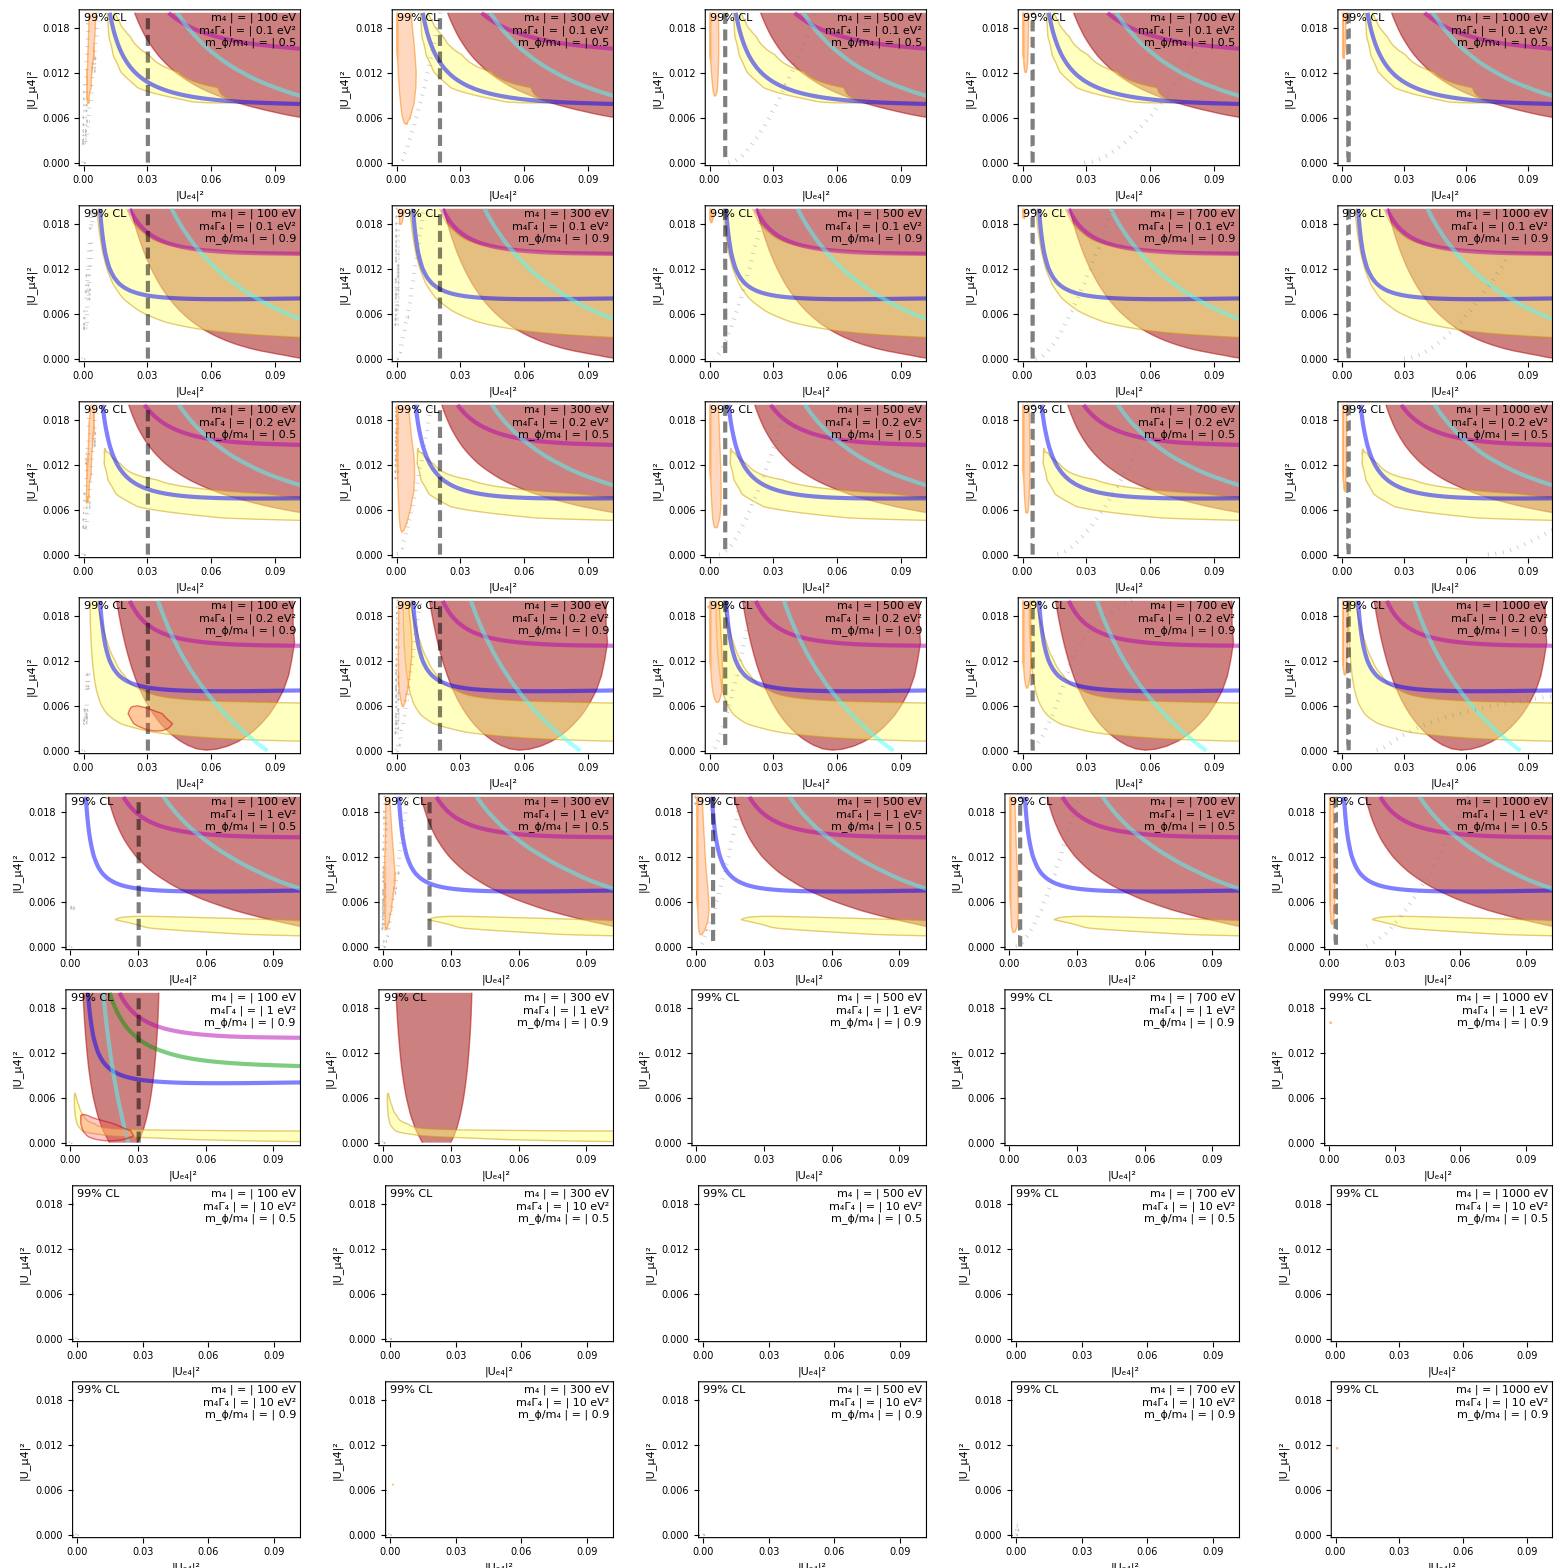

```mathematica
Grid[Table[
MyPlot[Sequence@@key,dm41Table⟦j⟧]=Show[MyPlot["lsnd-ivan",Sequence@@key,j],MyPlot["mbjk",Sequence@@key,j],MyPlot["opera",Sequence@@key,j],MyPlot["icarus",Sequence@@key,j],MyPlot["karmen-ivan",Sequence@@key,j],MyPlot["e776",Sequence@@key,j],MyPlot["betadecay",Sequence@@key,j],MyPlot["freestreaming",Sequence@@key,j],(*MyPlot["all",Sequence@@key,j],*)MyPlot["nocosmo",Sequence@@key,j],MyPlot["nolsnd",Sequence@@key,j],
PlotRange->{{0,.1},{0,.02}},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->{
Text[Framed["99% CL",Background->GrayLevel[1,.8]],Scaled[{0.02,0.98}],{-1,1}],
Inset[Framed[Grid[{
{"m_4","=",ToString[Round[Sqrt[dm41Table⟦j⟧]//.NN]]<>" eV"},
{"m_4Γ_4","=",If[key⟦1⟧=="1e4","10^4",ToString[m4Γ[Prepend[key⟦1;;2⟧,"mbjk"]]]]<>" eV^2"},
{"m_ϕ/m_4","=",ToString[mAm4[Prepend[key⟦1;;2⟧,"mbjk"]]]}
},Alignment->{{Right,Center,Left},{Baseline}},ItemSize->{Automatic,1.1},
Spacings->{{0.5,{0.2}},0.1}],Background->GrayLevel[1,.8]],Scaled[{0.98,0.98}],{1,1}]
}],{key,(*{{}}*)Union[RunList⟦;;-2,{2,3}⟧]},{j,1,Length[dm41Table]}]]
```

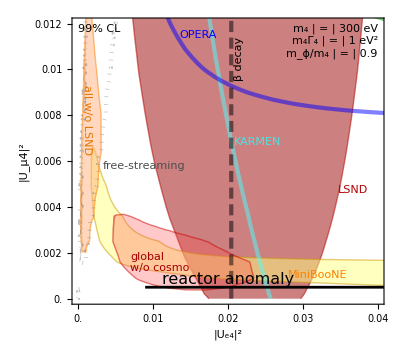
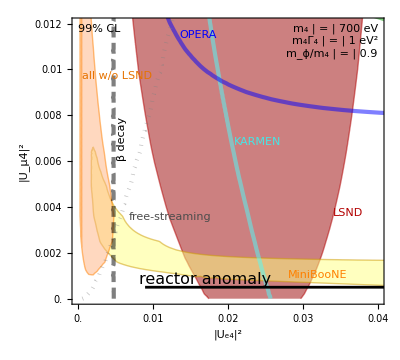
-Graphics-Dentler et al. 2019 | -Graphics-Dentler et al. 2019

Export::noopen: Cannot open Ue4Um4-300.pdf.

Export::noopen: Cannot open Ue4Um4-700.pdf.

```mathematica
(* reactor preferred region *)
Do[
DataReactor[k]=Cases[Import["~/Dropbox/neutrino-decay/Spectrum_MD/Dat/chi2_tab_"<>ToString[k]<>"_higher_x.dat","Table"],{Repeated[_?NumericQ]}]⟦All,1;;3⟧;
DataReactorInterpol[k]=Interpolation[DataReactor[k],InterpolationOrder->1];
Chi2MinReactor[k]=FindMinValue[DataReactorInterpol[k][0,Ue4sq],{Ue4sq,0.01}]//Quiet;
ConfIntReactor[k]={Ue4sq/.FindRoot[DataReactorInterpol[k][0.,Ue4sq]-Chi2MinReactor[k]==χ2[1,0.01],{Ue4sq,0.}]//Quiet,
Ue4sq/.FindRoot[DataReactorInterpol[k][0.,Ue4sq]-Chi2MinReactor[k]==χ2[1,0.01],{Ue4sq,0.2}]//Quiet},
{k,{300,700}}];

(* money plot *)
key={"1","0.9",2};
MyLegend2=Framed[Grid[{
{"m_4","=",ToString[Round[Sqrt[dm41Table⟦key⟦-1⟧⟧]//.NN]]<>" eV"},
{"m_4Γ_4","=",If[key⟦1⟧=="1e4","10^4",ToString[m4Γ[Prepend[key⟦1;;2⟧,"mbjk"]]]]<>" eV^2"},
{"m_ϕ/m_4","=",ToString[mAm4[Prepend[key⟦1;;2⟧,"mbjk"]]]}
},Alignment->{{Right,Center,Left},{Baseline}},ItemSize->{Automatic,1.1},
Spacings->{{0.5,{0.2}},0.1}],Background->GrayLevel[1,.8]];
h=Graphics[Line[{{0,-0.5},{0,0.5}}]];
ciReact=ConfIntReactor[Sqrt[dm41Table⟦key⟦-1⟧⟧]];
MyPlot[101]=Show[MyPlot["lsnd-ivan",Sequence@@key],MyPlot["mbjk",Sequence@@key],MyPlot["nolsnd",Sequence@@key],MyPlot["nocosmo",Sequence@@key],MyPlot["karmen-ivan",Sequence@@key],MyPlot["opera",Sequence@@key],MyPlot["icarus",Sequence@@key],MyPlot["e776",Sequence@@key],MyPlot["freestreaming",Sequence@@key],MyPlot["betadecay",Sequence@@key],
PlotRange->{{0,0.04},{0,.012}},ImagePadding->{{Automatic,Automatic},{Automatic,15}},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->Style[{
Text[Framed["99% CL",Background->GrayLevel[1,.8]],Scaled[{0.02,0.98}],{-1,1}],
MyStyle["lsnd-ivan"]⟦1,1⟧,Text["LSND",{0.0347,0.0045},{-1,-1},{0.22,1}],
Orange,Text[Style["MiniBooNE",Background->Lighter[MyStyle["mbjk"]⟦2,1⟧,.5]],{0.028,0.0008},{-1,-1},{1,-0.02}],
MyStyle["opera"]⟦1⟧,Text[Style["OPERA",Background->MyStyle["lsnd-ivan"]⟦2,1⟧],{0.0135,0.0113},{-1,-1},{1,-1}],
Darker[MyStyle["karmen-ivan"]⟦1,1⟧,.1],Text["KARMEN",{0.0208,0.0066},{-1,-1},{0.25,-1}],
(*MyStyle["betadecay"]⟦1⟧,Text["β decay",{0.0306,0.0027},{-1,1},{0,1}],*)
MyStyle["betadecay"]⟦1⟧,Text["β decay",{0.0208,0.0095},{-1,1},{0,1}],
(*Darker[MyStyle["nolsnd"]⟦1,1⟧,.1],Text["all w/o LSND",{0.00055,0.01},{-1,-1},{0,-1}],*)
Darker[MyStyle["nolsnd"]⟦1,1⟧,.1],Text["all w/o LSND",{0.0005,0.0093},{-1,-1},{0,-1}],
GrayLevel[.3],Text[Style["free-streaming",LineSpacing->{0.8,0}],{0.0033,0.006},{-1,1},{0.11,1}],
Darker[MyStyle["nocosmo"]⟦1,1⟧,.2],Text[Style["global\nw/o cosmo",LineSpacing->{1,0}],{0.007,0.0011},{-1,-1}],
(*Darker[MyStyle["e776"]⟦1,1⟧,.3],Text["E776",{0.035,0.0068},{-1,-1},{1,-0.03}],*)
Black,Dashing[{}],Arrowheads[{{Automatic,Automatic,h},{Automatic,Automatic,h}}],AbsoluteThickness[2],Arrow[{{ciReact⟦1⟧,0.0005},{ciReact⟦2⟧,0.0005}}],
Text[Style["reactor anomaly",FontSize->16],{0.02,0.0005},{-0.05,-1.1}],
Black,Dashing[{}],Inset[MyLegend2,Scaled[{0.98,0.98}],{1,1}]
},FontSize->17],PlotRangePadding->0];
tck=FrameTicks/.FullOptions[MyPlot[101]];
MyPlot[101]=Overlay[{JHEPPlot[Show[MyPlot[101],FrameTicks->ReplacePart[tck,1->tck⟦1⟧/.
{loc_,lab_,len:{_,_},sty_}:>{loc,If[ToExpression[lab]===Round[ToExpression[lab],0.01],lab,""],len,sty}]]],
Style["Dentler et al. 2019",FontFamily->"Helvetica",FontSize->14]},Alignment->{-0.45,1}];

key={"1","0.9",4};
ciReact=ConfIntReactor[Sqrt[dm41Table⟦key⟦-1⟧⟧]];
MyLegend2=Framed[Grid[{
{"m_4","=",ToString[Round[Sqrt[dm41Table⟦key⟦-1⟧⟧]//.NN]]<>" eV"},
{"m_4Γ_4","=",If[key⟦1⟧=="1e4","10^4",ToString[m4Γ[Prepend[key⟦1;;2⟧,"mbjk"]]]]<>" eV^2"},
{"m_ϕ/m_4","=",ToString[mAm4[Prepend[key⟦1;;2⟧,"mbjk"]]]}
},Alignment->{{Right,Center,Left},{Baseline}},ItemSize->{Automatic,1.1},
Spacings->{{0.5,{0.2}},0.1}],Background->GrayLevel[1,.8]];
MyPlot[102]=Show[MyPlot["lsnd-ivan",Sequence@@key],MyPlot["mbjk",Sequence@@key],MyPlot["nolsnd",Sequence@@key],MyPlot["nocosmo",Sequence@@key],MyPlot["karmen-ivan",Sequence@@key],MyPlot["opera",Sequence@@key],MyPlot["icarus",Sequence@@key],MyPlot["e776",Sequence@@key],MyPlot["freestreaming",Sequence@@key],MyPlot["betadecay",Sequence@@key],
PlotRange->{{0,0.04},{0,.012}},ImagePadding->{{Automatic,Automatic},{Automatic,15}},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->Style[{
Text[Framed["99% CL",Background->GrayLevel[1,.8]],Scaled[{0.02,0.98}],{-1,1}],
MyStyle["lsnd-ivan"]⟦1,1⟧,Text["LSND",{0.034,0.0035},{-1,-1},{0.22,1}],
Orange,Text[Style["MiniBooNE",Background->Lighter[MyStyle["mbjk"]⟦2,1⟧,.5]],{0.028,0.0008},{-1,-1},{1,-0.02}],
MyStyle["opera"]⟦1⟧,Text[Style["OPERA",Background->MyStyle["lsnd-ivan"]⟦2,1⟧],{0.0135,0.0113},{-1,-1},{1,-1}],
Darker[MyStyle["karmen-ivan"]⟦1,1⟧,.1],Text["KARMEN",{0.0208,0.0066},{-1,-1},{0.25,-1}],
MyStyle["betadecay"]⟦1⟧,Text["β decay",{0.0052,0.006},{-1,1},{0,1}],
Darker[MyStyle["nolsnd"]⟦1,1⟧,.1],Text["all w/o LSND",{0.0005,0.0095},{-1,-1},{0.04,-1}],
GrayLevel[.3],Text[Style[Style["free-streaming",Background->GrayLevel[1,.7]],LineSpacing->{0.8,0}],{0.0068,0.0038},{-1,1},{0.27,1}],
(*Darker[MyStyle["nocosmo"]⟦1,1⟧,.2],Text[Style["global\nw/o cosmo",LineSpacing->{1,0}],{0.008,0.0009},{-1,-1}],*)
(*MyStyle["e776"]⟦1,1⟧,Text["E776 (4 dof)",{0.0215,0.0113},{-1,-1},{1,-0.6}],*)
Black,Dashing[{}],Arrowheads[{{Automatic,Automatic,h},{Automatic,Automatic,h}}],AbsoluteThickness[2],Arrow[{{ciReact⟦1⟧,0.0005},{ciReact⟦2⟧,0.0005}}],
Text[Style["reactor anomaly",FontSize->16],{0.017,0.0005},{-0.05,-1.1}],
Black,Dashing[{}],Inset[MyLegend2,Scaled[{0.98,0.98}],{1,1}]
},FontSize->17],PlotRangePadding->0];
tck=FrameTicks/.FullOptions[MyPlot[102]];
MyPlot[102]=Overlay[{JHEPPlot[Show[MyPlot[102],FrameTicks->ReplacePart[tck,1->tck⟦1⟧/.
{loc_,lab_,len:{_,_},sty_}:>{loc,If[ToExpression[lab]===Round[ToExpression[lab],0.01],lab,""],len,sty}]]],
Style["Dentler et al. 2019",FontFamily->"Helvetica",FontSize->14]},Alignment->{-0.45,1}];
Grid[{{MyPlot[101],MyPlot[102]}}]
Export["Ue4Um4-300.pdf",MyPlot[101]];
Export["Ue4Um4-700.pdf",MyPlot[102]];
```

```mathematica
k={"1","0.9"};
t=globalChi2Min[{"all",Sequence@@k}]-globalChi2Min[{"nolsnd",Sequence@@k}]-globalChi2Min[{"lsnd-ivan",Sequence@@k}];
Print["Δχ^2(global - nolsnd - lsnd) = ",t,"; p-value(PG) = ",xx//.FindRoot[χ2[5,xx]==Abs[t],{xx,1*^-4}]//Quiet,
", (", xx//.FindRoot[χ2[5,PValue[xx]]==Abs[t],{xx,4}]//Quiet,"σ)"];

t=globalChi2Min[{"all",Sequence@@k}]-globalChi2Min[{"nocosmo",Sequence@@k}];
Print["Δχ^2(global - nocosmo) = ",t];

DataFilesExtra={"8-oscdecay/bfp-noaux.dat.gz","8-oscdecay/bfp-nolsnd-noaux.dat.gz"};
For[j=1,j≤Length[DataFilesExtra],j++,
i=700+j-1;
DataRawBFP[i]=Import[DataFilesExtra⟦j⟧,"Text"];
DataBFP[i]=Cases[ImportString[DataRawBFP[i],"Table"],{Repeated[_?NumericQ]}];
globalChi2Min[i]=Min[DataBFP[i]⟦All,{-2,-1}⟧];
(globalBFP[i][#⟦1⟧]=#⟦2⟧)&/@Partition[ImportString[StringCases[DataRawBFP[i],Shortest["Best grid point NH "~~x__~~"\n"]:>x]⟦1⟧,"Table"]⟦1⟧,2];
];

t=globalChi2Min[700]-globalChi2Min[701]-globalChi2Min[{"lsnd-ivan",Sequence@@k}];
Print["Δχ^2(global - nolsnd - lsnd; noaux) = ",t,"; p-value(PG) = ",xx//.FindRoot[χ2[5,xx]==Abs[t],{xx,1*^-4}]//Quiet,
", (", xx//.FindRoot[χ2[5,PValue[xx]]==Abs[t],{xx,4}]//Quiet,"σ)"]

kk={"nocosmo",Sequence@@k};
Print["bfp all w/o cosmo: ",{Sqrt[N[globalBFP[kk]["DM41"]]],(globalBFP[kk]["Ue4"])^2,(globalBFP[kk]["Um4"])^2,globalBFP[kk]["M4_GAMMA"],globalBFP[kk]["MA_OVER_M4"]}];
```

Δχ^2(global - nolsnd - lsnd) = 33.4186; p-value(PG) = 3.10749×10^-6, (4.66358σ)

Δχ^2(global - nocosmo) = 15.5502

Δχ^2(global - nolsnd - lsnd; noaux) = 11.825; p-value(PG) = 0.0372663, (2.08283σ)

bfp all w/o cosmo: {97.0249,0.0180365,0.00150648,0.871435,0.888247}

### Plots not used for the paper (partly outdated)

#### Δm_41^2 vs. U_e4^2 vs. U_μ4^2

```mathematica
Clear[DataFiles];
ExpList={"lsnd-ivan","karmen-ivan","mbjk","opera","icarus","e776","all"};

(* small-Subscript[m, 4] window *)
(*Ext="-dirac.dat.gz";
M4GList={"0.1","0.2","1","2","10"};
MAM4List={"0.1","0.5","0.7","0.9"};
dm41Table={1.,2.5,100.};
MyContours2dof={χ2[2,PValue[2]],χ2[2,PValue[3]]};
MyContours5dof={χ2[5,PValue[2]],χ2[5,PValue[3]]};
RunList=Flatten[Outer[List,ExpList,M4GList,MAM4List],2];
RunList=Append[RunList,{"app-proj"}];
For[i=1,i≤Length[RunList],i++,
If[Length[RunList⟦i⟧]>1, (* slices through parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>"-m4G"<>RunList⟦i,2⟧<>"-MAM4"<>RunList⟦i,3⟧<>Ext,
(* Else - projections over parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>Ext;
];
DataFilesBFP[i]="8-oscdecay/bfp-"<>RunList⟦i,1⟧<>Ext;
If[FileExistsQ[StringReplace[DataFiles[i],Ext->"-hires"<>Ext]],
DataFiles[i]=StringReplace[DataFiles[i],Ext->"-hires"<>Ext];
];
];*)

(* intermediate-Subscript[m, 4] window *)
Suffix=".dat";
M4GList={"0.1","0.2","1","2","10"};
MAM4List={"0.1","0.5","0.7","0.9"};
MyContours2dof={χ2[2,PValue[2]],χ2[2,PValue[3]]};
MyContours5dof={χ2[5,PValue[2]],χ2[5,PValue[3]]}; (* no sensitivity to Subscript[m, 4] from oscillation, but from β decay/cosmo *)
RunList=Flatten[Outer[List,ExpList,M4GList,MAM4List],2];
(*RunList=Append[RunList,{"app-proj"}];*)
For[i=1,i≤Length[RunList],i++,
If[Length[RunList⟦i⟧]>1, (* slices through parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>"-m4G"<>RunList⟦i,2⟧<>"-MAM4"<>RunList⟦i,3⟧<>Suffix,
(* Else - projections over parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>Suffix;
];
DataFilesBFP[i]="8-oscdecay/bfp-"<>RunList⟦i,1⟧<>Suffix;
];

(* large-Subscript[m, 4] window *)
(*Suffix="-largem4.dat.gz";
(*M4GList={"0.1","0.2","1","2","10"};
MAM4List={"0.1","0.5","0.7","0.9"};*)
M4GList={"1e4"};
MAM4List={"0.9"};
AppendTo[ExpList,"app-nolsnd"];
dm41Table={2.5*^9};
MyContours2dof={χ2[2,PValue[2]],χ2[2,PValue[3]]};
MyContours5dof={χ2[4,PValue[2]],χ2[4,PValue[3]]}; (* no sensitivity to Subscript[m, 4] in the large Subscript[m, 4] limit -> only 4 dof *)
RunList=Flatten[Outer[List,ExpList,M4GList,MAM4List],2];
(*RunList=Append[RunList,{"app-proj"}];*)
For[i=1,i≤Length[RunList],i++,
If[Length[RunList⟦i⟧]>1, (* slices through parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>"-m4G"<>RunList⟦i,2⟧<>"-MAM4"<>RunList⟦i,3⟧<>Suffix,
(* Else - projections over parameter space *)
DataFiles[i]="8-oscdecay/dm41Ue4Um4-"<>RunList⟦i,1⟧<>Suffix;
];
DataFilesBFP[i]="8-oscdecay/bfp-"<>RunList⟦i,1⟧<>Suffix;
];*)

Clear[mAm4,m4Γ,thisChi2Min,globalChi2Min,thisBFP,globalBFP,DataInterpol,DataReducedInterpol];
AllData=ParallelTable[Import[DataFiles[i],"Text"],{i,1,Length[RunList]}];
For[i=1,i≤Length[AllData],i++,
key=RunList⟦i⟧;
WriteString["stdout","Reading sample "<>ToString[key]<>" from "<>DataFiles[i]<>" ..."];
DataRaw[i]=AllData⟦i⟧;
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,Min[#⟦-2⟧,#⟦-1⟧]}&/@Cases[ImportString[DataRaw[i],"Table"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

(* project onto Ue4-Um4 plane gathering elements with same Subscript[U, e4] and Subscript[U, μ4], then pick the Subscript[Δm, 41]^2 with the minimal χ^2 *)
DataReduced[i]=First[Sort[#,#1⟦-1⟧<#2⟦-1⟧&]]&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];
DataReduced[i]={#⟦2⟧,#⟦3⟧,#⟦-1⟧}&/@DataReduced[i];
DataReducedInterpol[i]=Interpolation[DataReduced[i],InterpolationOrder->1];

logdm41Min=Min[Data[i]⟦All,1⟧];
logdm41Max=Max[Data[i]⟦All,1⟧];
Ue4Min[i]=Min[Data[i]⟦All,2⟧];
Ue4Max[i]=Max[Data[i]⟦All,2⟧];
Um4Min[i]=Min[Data[i]⟦All,3⟧];
Um4Max[i]=Max[Data[i]⟦All,3⟧];
thisChi2Min[i]=Min[Data[i]⟦All,-1⟧];
(thisBFP[i][#⟦1⟧]=#⟦2⟧)&/@Partition[ImportString[StringCases[DataRaw[i],Shortest["Best grid point NH "~~x__~~"\n"]:>x]⟦1⟧,"Table"]⟦1⟧,2];

ExtractParam[s_,param_String]:=ToExpression[StringReplace[s,RegularExpression["(?m)(?s).*# *"<>param<>" = ([-+0-9eE\\.]*).*"]:>"$1"]];
m4Γ[i]=ExtractParam[DataRaw[i],"M4_GAMMA"];
mAm4[i]=ExtractParam[DataRaw[i],"MA_OVER_M4"];

(* read best fit point *)
DataRawBFP[i]=Import[DataFilesBFP[i],"Text"];
DataBFP[i]=Cases[ImportString[DataRawBFP[i],"Table"],{Repeated[_?NumericQ]}];
globalChi2Min[i]=Min[DataBFP[i]⟦All,{-2,-1}⟧];
(globalBFP[i][#⟦1⟧]=#⟦2⟧)&/@Partition[ImportString[StringCases[DataRawBFP[i],Shortest["Best grid point NH "~~x__~~"\n"]:>x]⟦1⟧,"Table"]⟦1⟧,2];

(* For testing purposes: as E776 exhibits a spurious best fit point at very large Ue4 (rules out by reactor+solar), we normalize against the no-oscillation hypothesis instead. DO NOT USE FOR PUBLICATION *)
If[key⟦1⟧=="e776",
thisChi2Min[i]=globalChi2Min[i]=DataInterpol[i][0.,0.,0.]];

mAm4[key]=mAm4[i];
m4Γ[key]=m4Γ[i];
thisChi2Min[key]=thisChi2Min[i];
globalChi2Min[key]=globalChi2Min[i];
thisBFP[key][p_]=thisBFP[i][p];
globalBFP[key][p_]=globalBFP[i][p];
DataInterpol[key]=DataInterpol[i];
DataReducedInterpol[key]=DataReducedInterpol[i];
WriteString["stdout","   χ2min = "<>ToString[FortranForm[thisChi2Min[i]]]<>
", χ2global = "<>ToString[FortranForm[globalChi2Min[i]]]<>"\n"];
];
```

```mathematica
MyStyle["mbjk"]={{Directive[Orange],Directive[Orange,Dashed]},{RGBColor[1,1,.5,.5],RGBColor[1,1,.8,.5],None}};
MyStyle["opera"]={Directive[AbsoluteThickness[3],Blue],Directive[AbsoluteThickness[3],Blue,Dashed]};
MyStyle["icarus"]={Directive[AbsoluteThickness[3],RGBColor[.7,0,.7]],Directive[AbsoluteThickness[3],RGBColor[.7,0,.7],Dashed]};
MyStyle["e776"]={Directive[RGBColor[0,.6,0],AbsoluteThickness[3]],Directive[RGBColor[0,.6,0],AbsoluteThickness[3],Dashed]};
MyStyle["lsnd-ivan"]={{Directive[RGBColor[.7,0,0]],Directive[RGBColor[.7,0,0],Dashed]},{RGBColor[.8,.5,.5],RGBColor[.8,.6,.6],None}};
MyStyle["karmen-ivan"]={Directive[RGBColor[.3,1,1],AbsoluteThickness[3]],Directive[RGBColor[.3,1,1],AbsoluteThickness[3],Dashed]};
MyStyle["all"]={{Directive[RGBColor[0.8,0,0]],Directive[RGBColor[0.8,0,0],Dashed]},{RGBColor[1,.3,.3,.5],RGBColor[1,.4,.4,.5],None}};
MyStyle["all-proj"]={Directive[AbsoluteThickness[3],Red],Directive[AbsoluteThickness[3],Red,Dashed]};

Um42Limit=0.00711; (* limit on |Subscript[U, μ4]|^2 to show in the plots *)
Ue42Limit=0.05366; (* limit on |Subscript[U, μ4]|^2 to show in the plots *)

dm41Table={1.*^4,1.*^5,1.*^6};
For[i=1,i≤Length[AllData],i++,
If[Head[MyStyle[RunList⟦i,1⟧]⟦1⟧]===List,
For[j=1,j≤Length[dm41Table],j++,
MyPlot[Sequence@@RunList⟦i⟧,j]=ContourPlot[DataInterpol[i][Log10[dm41Table⟦j⟧],Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours5dof,ContourShading->MyStyle[RunList⟦i,1⟧]⟦2⟧,ContourStyle->MyStyle[RunList⟦i,1⟧]⟦1⟧(*,PlotPoints->50*)]
];
MyPlot[Sequence@@RunList⟦i⟧]=ContourPlot[DataReducedInterpol[i][Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours2dof,ContourShading->MyStyle[RunList⟦i,1⟧]⟦2⟧,ContourStyle->MyStyle[RunList⟦i,1⟧]⟦1⟧(*,PlotPoints->50*)],

(* Else *)
For[j=1,j≤Length[dm41Table],j++,
MyPlot[Sequence@@RunList⟦i⟧,j]=ContourPlot[DataInterpol[i][Log10[dm41Table⟦j⟧],Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours5dof,ContourShading->False,
ContourStyle->MyStyle[RunList⟦i,1⟧](*,PlotPoints->50*)]
];
MyPlot[Sequence@@RunList⟦i⟧]=ContourPlot[DataReducedInterpol[i][Sqrt[Ue4sq],Sqrt[Uμ4sq]]-globalChi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.02},PlotRange->All,Contours->MyContours2dof,ContourShading->False,
ContourStyle->MyStyle[RunList⟦i,1⟧](*,PlotPoints->50*)];
]; (* If[MyStyles] *)
]; (* For[i] - AllData *)
```

```mathematica
Grid[Table[
Show[MyPlot["lsnd-ivan",Sequence@@key,j],MyPlot["opera",Sequence@@key,j],MyPlot["icarus",Sequence@@key,j],MyPlot["karmen-ivan",Sequence@@key,j],MyPlot["e776",Sequence@@key,j],MyPlot["mbjk",Sequence@@key,j],MyPlot["all",Sequence@@key,j],(*MyPlot["all-proj"],*)
PlotRange->{{0,.2},{0,.02}},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->{
(*Black,Text["90%, 99% C.L.",Scaled[{0.97,0.97}],{1,1}],*)
Text["Δm_41^2 = "<>ToString[FortranForm[dm41Table⟦j⟧]]<>" eV^2",Scaled[{0.97,0.9}],{1,1}],
Text["m_4Γ = "<>ToString[m4Γ[Prepend[key,"opera"]]]<>" eV^2",Scaled[{0.97,0.82}],{1,1}],
Text["m_A'/m_4 = "<>ToString[mAm4[Prepend[key,"opera"]]],Scaled[{0.97,0.72}],{1,1}],
Black,Arrow[{{0.005,Um42Limit},{0.005,Um42Limit+0.004}}],
Arrow[{{0.195,Um42Limit},{0.195,Um42Limit+0.004}}],
{AbsoluteThickness[3],Line[{{-1,Um42Limit},{1,Um42Limit}}]},
Text["excluded by ν_μ disapp.",{0.19,Um42Limit},{1,-1.2},Background->GrayLevel[1,.7]]
(*Arrow[{{Ue42Limit,0.001},{Ue42Limit+0.03,0.001}}],
Arrow[{{Ue42Limit,0.019},{Ue42Limit+0.03,0.019}}],
{AbsoluteThickness[3],Line[{{Ue42Limit,-1},{Ue42Limit,1}}]},
Text["excluded by ν_e disapp.",{Ue42Limit,0.017},{1,1.4},{0,1},Background->GrayLevel[1,.7]]*)
}],{key,(*{{}}*)Union[RunList⟦;;-2,{2,3}⟧]},{j,1,Length[dm41Table]}]]
```

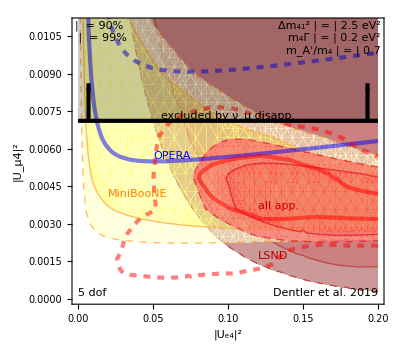

```mathematica
(* money plot for small Subscript[m, 4] *)
If[Max[dm41Table]<1000.,
j=2;
key={"0.2","0.7"};
MyLegend1=Framed[Grid[{
{"Δm_41^2","=",ToString[dm41Table⟦j⟧]<>" eV^2"},
{"m_4Γ","=",ToString[m4Γ[Prepend[key,"mbjk"]]]<>" eV^2"},
{"m_A'/m_4","=",ToString[mAm4[Prepend[key,"mbjk"]]]}
},Alignment->{{Right,Center,Left},{Baseline}},ItemSize->{Automatic,1.1},
Spacings->{{0.5,{0.2}},0.1}],Background->GrayLevel[1,.8]];
MyLegend2=Framed[Grid[{
{Show[LegendLine[Directive[Black,AbsoluteThickness[2.5]]],ImageSize->20]," = 2σ "},
{Show[LegendLine[Directive[Black,AbsoluteThickness[2.5],Dotted]],ImageSize->20]," = 3σ"}
},Alignment->{Left,Center},Spacings->{{1.,{0},0.1},Automatic}],Background->GrayLevel[1,.8]];
Show[MyPlot["lsnd-ivan",Sequence@@key,j],MyPlot["mbjk",Sequence@@key,j],MyPlot["app",Sequence@@key,j],
MyPlot["opera",Sequence@@key,j],MyPlot["icarus",Sequence@@key,j],MyPlot["e776",Sequence@@key,j],MyPlot["app-proj"],
PlotRange->{{0,.2},{0,.011}},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->Style[{
GrayLevel[0,.2],Rectangle[{0,Um42Limit},{0.2,1}],GrayLevel[0,1],
Inset[MyLegend1,Scaled[{0.99,0.99}],{1,1}],
Inset[MyLegend2,Scaled[{0.01,0.99}],{-1,1}],
MyStyle["lsnd-ivan"]⟦1,1⟧,Text["LSND",{0.12,0.0015},{-1,-1},{1,-0.4}],
MyStyle["mbjk"]⟦1,1⟧,Text["MiniBooNE",{0.02,0.004},{-1,-1},{1,-0.3}],
MyStyle["opera"]⟦1⟧,Text["OPERA",{0.05,0.0055},{-1,-1},{1,0.08}],
(*MyStyle["e776"]⟦1⟧,Text["E776",{0.14,0.0059},{-1,-1},{1,-0.15}],*)
MyStyle["app"]⟦1,1⟧,Text["all app.",{0.12,0.0035},{-1,-1}],
Black,Arrow[{{0.007,Um42Limit},{0.007,Um42Limit+0.0015}}],
Arrow[{{0.193,Um42Limit},{0.193,Um42Limit+0.0015}}],
{AbsoluteThickness[3],Line[{{0,Um42Limit},{0.2,Um42Limit}}]},
Text["excluded by ν_μ disapp.",{0.1,Um42Limit},{0,-1.2},Background->GrayLevel[1,.7]],
Text["5 dof",Scaled[{0.02,0.02}],{-1,-1}],
Text["Dentler et al. 2019",Scaled[{0.98,0.02}],{1,-1}]
},FontSize->17],PlotRangePadding->0]
]
```

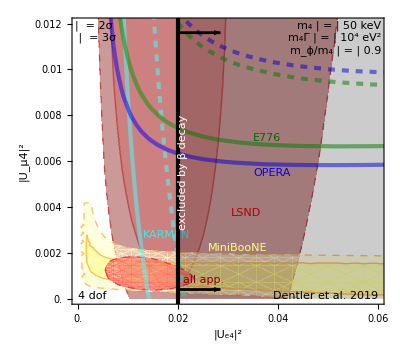

```mathematica
(* money plots for large Subscript[m, 4] *)
Ue42Limit=0.02; (* limit on |Subscript[U, μ4]|^2 to show in the plots (kinematic constraint from arxiv:1504.07496 *)
If[Max[dm41Table]>1000.,
j=1;
key={"0.2","0.7"};
MyLegend1=Framed[Grid[{
{"m_4","=",ToString[Sqrt[dm41Table⟦j⟧]/keV//.NN]<>" keV"},
{"m_4Γ","=",ToString[m4Γ[Prepend[key,"mbjk"]]]<>" eV^2"},
{"m_ϕ/m_4","=",ToString[mAm4[Prepend[key,"mbjk"]]]}
},Alignment->{{Right,Center,Left},{Baseline}},ItemSize->{Automatic,1.1},
Spacings->{{0.5,{0.2}},0.1}],Background->GrayLevel[1,.8]];
MyLegend2=Framed[Grid[{
{Show[LegendLine[Directive[Black,AbsoluteThickness[2.5]]],ImageSize->20]," = 2σ "},
{Show[LegendLine[Directive[Black,AbsoluteThickness[2.5],Dotted]],ImageSize->20]," = 3σ"}
},Alignment->{Left,Center},Spacings->{{1.,{0},0.1},Automatic}],Background->GrayLevel[1,.8]];
(*MyPlot[101]=Show[MyPlot["lsnd-ivan",Sequence@@key,j],MyPlot["mbjk",Sequence@@key,j],MyPlot["app",Sequence@@key,j],
MyPlot["opera",Sequence@@key,j],MyPlot["icarus",Sequence@@key,j],MyPlot["e776",Sequence@@key,j],(*MyPlot["app-proj"],*)
PlotRange->{{0,.2},{0,.011}},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->Style[{
(*GrayLevel[0,.2],Rectangle[{0,Um42Limit},{0.2,1}],GrayLevel[0,1],*)
Inset[MyLegend1,Scaled[{0.99,0.99}],{1,1}],
Inset[MyLegend2,Scaled[{0.01,0.99}],{-1,1}],
MyStyle["lsnd-ivan"]⟦1,1⟧,Text[Style["LSND",Background->MyStyle["lsnd-ivan"]⟦2,2⟧],{0.13,0.0015},{-1,-1},{1,-0.4}],
MyStyle["mbjk"]⟦1,1⟧,Text[Style["MiniBooNE",Background->Directive[Lighter[MyStyle["mbjk"]⟦2,1⟧,.5],Opacity[1]]],{0.012,0.0053},{-1,-1},{1,-0.7}],
MyStyle["opera"]⟦1⟧,Text["OPERA",{0.05,0.0058},{-1,-1},{1,0.08}],
(*MyStyle["e776"]⟦1⟧,Text["E776",{0.14,0.0059},{-1,-1},{1,-0.15}],*)
MyStyle["app"]⟦1,1⟧,Text["all app.",{0.15,0.0035},{-1,-1}],
Black,(*Arrow[{{0.007,Um42Limit},{0.007,Um42Limit+0.0015}}],
Arrow[{{0.193,Um42Limit},{0.193,Um42Limit+0.0015}}],
{AbsoluteThickness[3],Line[{{0,Um42Limit},{0.2,Um42Limit}}]},
Text["excluded by ν_μ disapp.",{0.1,Um42Limit},{0,-1.2},Background->GrayLevel[1,.7]],*)
Text["4 dof",Scaled[{0.02,0.02}],{-1,-1}],
Text["Dentler et al. 2019",Scaled[{0.98,0.02}],{1,-1}]
},FontSize->17],PlotRangePadding->0];*)

key={"1e4","0.9"};
MyLegend1=Framed[Grid[{
{"m_4","=",ToString[Round[Sqrt[dm41Table⟦j⟧]/keV//.NN]]<>" keV"},
{"m_4Γ","=",If[key⟦1⟧=="1e4","10^4",ToString[m4Γ[Prepend[key,"mbjk"]]]]<>" eV^2"},
{"m_ϕ/m_4","=",ToString[mAm4[Prepend[key,"mbjk"]]]}
},Alignment->{{Right,Center,Left},{Baseline}},ItemSize->{Automatic,1.1},
Spacings->{{0.5,{0.2}},0.1}],Background->GrayLevel[1,.8]];
MyPlot[102]=JHEPPlot[Show[MyPlot["lsnd-ivan",Sequence@@key,j],MyPlot["mbjk",Sequence@@key,j],MyPlot["app",Sequence@@key,j],MyPlot["karmen-ivan",Sequence@@key,j],
MyPlot["opera",Sequence@@key,j],(*MyPlot["icarus",Sequence@@key,j],*)MyPlot["e776",Sequence@@key,j],
PlotRange->{{0,0.06},{0,.012}},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->Style[{
(*GrayLevel[0,.2],Rectangle[{0,Um42Limit},{0.2,1}],*)
GrayLevel[0,.2],Rectangle[{Ue42Limit,0},{1,0.2}],GrayLevel[0,1],
Black,{AbsoluteThickness[2],Arrow[{{Ue42Limit,0.0004},{Ue42Limit+0.0085,0.0004}}],
Arrow[{{Ue42Limit,0.0116},{Ue42Limit+0.0085,0.0116}}]},
{AbsoluteThickness[3],Line[{{Ue42Limit,-1},{Ue42Limit,1}}]},
Text[Style[" excluded by β decay ",White],{Ue42Limit,0.003},{-1,1.4},{0,1}],
Text["4 dof",Scaled[{0.02,0.01}],{-1,-1}],
Text[Style["Dentler et al. 2019"],Scaled[{0.98,0.01}],{1,-1}],
MyStyle["lsnd-ivan"]⟦1,1⟧,Text["LSND",{0.0305,0.0035},{-1,-1},{0.2,1}],
MyStyle["mbjk"]⟦1,1⟧,(*Text[Style["MiniBooNE",Background->Directive[Lighter[MyStyle["mbjk"]⟦2,1⟧,.5],Opacity[1]]],{0.001,0.0046},{1,-1},{0.3,-4}],*)
MyStyle["mbjk"]⟦2,1⟧,Opacity[1.],Text[Style["MiniBooNE"],{0.026,0.002},{-1,-1},{1,-0.02}],
MyStyle["opera"]⟦1⟧,Text["OPERA",{0.035,0.0057},{-1,1},{1,-0.03}],
Darker[MyStyle["karmen-ivan"]⟦1,1⟧,.1],Text["KARMEN",{0.013,0.003},{-1,1},{-0.1,1}],
Darker[MyStyle["e776"]⟦1,1⟧,.3],Text["E776",{0.035,0.0068},{-1,-1},{1,-0.03}],
Darker[MyStyle["app"]⟦1,1,1⟧,0.3],Text["all app.",{0.021,0.0006},{-1,-1}],
Black,Inset[MyLegend1,Scaled[{0.99,0.99}],{1,1}],
Inset[MyLegend2,Scaled[{0.01,0.99}],{-1,1}]
},FontSize->17],PlotRangePadding->0]];
];
Grid[{{(*MyPlot[101],*)MyPlot[102]}}]
```

```mathematica
k={"app",Sequence@@key};

(* difference in chi^2 between best fit along this slice and the global best fit *)
Print["Δχ^2(slice - global) = ",thisChi2Min[k]-globalChi2Min[k],
" p-value: ",(xx/.FindRoot[χ2[4,xx]==thisChi2Min[k]-globalChi2Min[k],{xx,0.05}]//Quiet),
 ", (",(xx/.FindRoot[χ2[4,PValue[xx]]==thisChi2Min[k]-globalChi2Min[k],{xx,2.}]//Quiet)," σ)"];

(* global best fit point *)
Print["global bfp: ",{(globalBFP[k]["Ue4"])^2,(globalBFP[k]["Um4"])^2,globalBFP[k]["M4_GAMMA"],globalBFP[k]["MA_OVER_M4"]}];
```

Δχ^2(slice - global) = 9.66312 p-value: 0.0465013, (1.99081 σ)

global bfp: {0.102079,0.00184918,31.4918,0.121418}

```mathematica
p=(thisBFP[{"mb-lsnd",Sequence@@key}][#]&/@{"DM41","Ue4","Um4"});
DataInterpol[{"mbjk",Sequence@@key}][Sequence@@p]+DataInterpol[{"lsnd-ivan",Sequence@@key}][Sequence@@p]
thisBFP[{"mbjk",Sequence@@key}]["chi^2"]+thisBFP[{"lsnd-ivan",Sequence@@key}]["chi^2"]
%-%%
FindRoot[χ2[4,PValue[xx]]==Abs[%],{xx,2.}]//Quiet
```

345.572

333.102

-12.4697

{xx→2.45268}

```mathematica
thisUe4=Sqrt[0.1];
MyContours2dof={χ2[2,0.01]};
MyContours5dof={χ2[5,0.01]};
(*MyContours2dof={χ2[2,PValue[2]]};
MyContours5dof={χ2[5,PValue[2]]};*)

For[i=1,i≤Length[RunList],i++,
(* project by gathering elements with same Subscript[Δm, 41]^2 and Subscript[U, μ4], then pick the Subscript[U, e4] with the minimal χ^2 *)
DataReduced[i]=First[Sort[#,#1⟦-1⟧<#2⟦-1⟧&]]&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
DataReduced[i]={#⟦1⟧,Log10[Max[(#⟦3⟧)^2,1*^-10]],#⟦-1⟧}&/@DataReduced[i];

(* pick data at given Subscript[U, e4] *)
DataReduced[i]={#⟦1⟧,Log10[Max[(#⟦2⟧)^2,1*^-10]],DataInterpol[i][#⟦1⟧,thisUe4,#⟦2⟧]}&/@Union[Data[i]⟦All,{1,3}⟧];
(*thisChi2Min[i]=Min[DataReduced[i]⟦All,-1⟧];*)

DataReducedInterpol[i]=Interpolation[DataReduced[i],InterpolationOrder->1];
If[Head[MyStyle[RunList⟦i,1⟧]⟦1⟧]===List,
MyPlot[Sequence@@RunList⟦i⟧]=ContourPlot[DataReducedInterpol[i][logdm41,logUm4sq]-globalChi2Min[i],{logUm4sq,-3.5,-0.5},{logdm41,-2,2},PlotRange->Full,Contours->MyContours5dof,ContourShading->{MyStyle[RunList⟦i,1⟧]⟦2,1⟧,None},ContourStyle->{MyStyle[RunList⟦i,1⟧]⟦1,1⟧}],
(* Else *)
MyPlot[Sequence@@RunList⟦i⟧]=ContourPlot[DataReducedInterpol[i][logdm41,logUm4sq]-globalChi2Min[i],{logUm4sq,-3.5,-0.5},{logdm41,-2,2},PlotRange->Full,Contours->MyContours5dof,ContourShading->False,ContourStyle->{MyStyle[RunList⟦i,1⟧]⟦1⟧}]
]
];
```

InterpolatingFunction::dmval: Input value {-1.99971,-3.49979} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(* load Mona's exclusion limit *)
ExtKeys={"cdhs","Minos","atm","mb200dis","noevid_noIC2"};
MyStyle["cdhs"]={Directive[AbsoluteThickness[3],RGBColor[0,.9,0]],Directive[AbsoluteThickness[3],RGBColor[0,.9,0],Dashed]};
MyStyle["mb200dis"]={Directive[AbsoluteThickness[3],RGBColor[0,.3,0]],Directive[AbsoluteThickness[3],RGBColor[0,.3,0],Dashed]};
MyStyle["Minos"]={Directive[AbsoluteThickness[3],RGBColor[.2,.2,.8]],Directive[AbsoluteThickness[3],RGBColor[.2,.2,.8],Dashed]};
MyStyle["atm"]={Directive[AbsoluteThickness[3],RGBColor[0,.8,.8]],Directive[AbsoluteThickness[3],RGBColor[0,.8,.8],Dashed]};
MyStyle["noevid_noIC2"]={Directive[AbsoluteThickness[3],Black],Directive[AbsoluteThickness[3],Black,Dashed]};

DataFilesExt="../mona/DataPedroNumu/"<>#<>".dat"&/@ExtKeys;
For[i=1,i≤Length[DataFilesExt],i++,
key=ExtKeys⟦i⟧;
DataExt[i]=Cases[Import[DataFilesExt⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataExtInterpol[i]=Interpolation[DataExt[i],InterpolationOrder->1];
Chi2MinExt[i]=Min[DataExt[i]⟦All,-1⟧];
If[Head[MyStyle[key]⟦1⟧]===List,
MyPlot[key]=ContourPlot[DataExtInterpol[i][logUm4sq,logdm41]-Chi2MinExt[i],{logUm4sq,-3.5,-0.5},{logdm41,-2,2},PlotRange->Full,Contours->MyContours2dof,ContourShading->{MyStyle[key]⟦2,1⟧,None},ContourStyle->{MyStyle[RunList⟦i,1⟧]⟦1,1⟧}],
(* Else *)
MyPlot[key]=ContourPlot[DataExtInterpol[i][logUm4sq,logdm41]-Chi2MinExt[i],{logUm4sq,-3.5,-0.5},{logdm41,-2,2},PlotRange->Full,Contours->MyContours2dof,ContourShading->False,ContourStyle->{MyStyle[key]⟦1⟧}]
]
];
```

InterpolatingFunction::dmval: Input value {-3.49979,-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

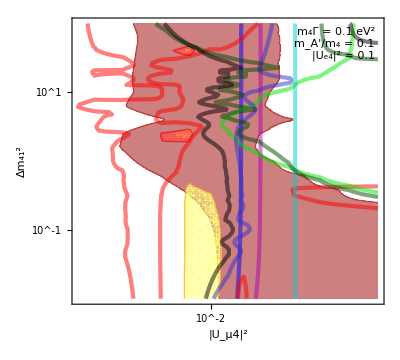
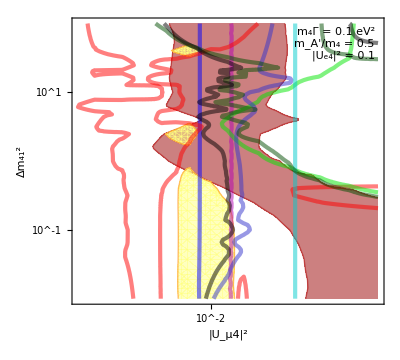
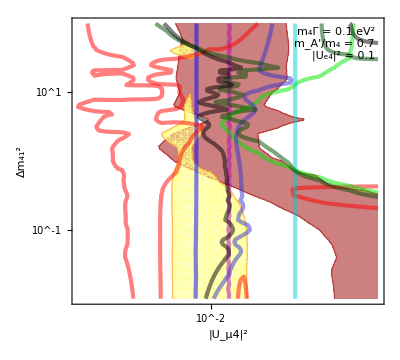
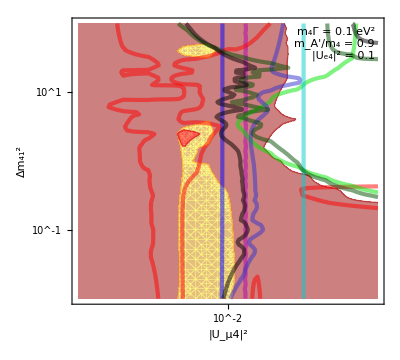
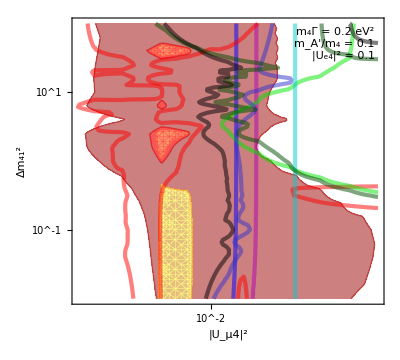
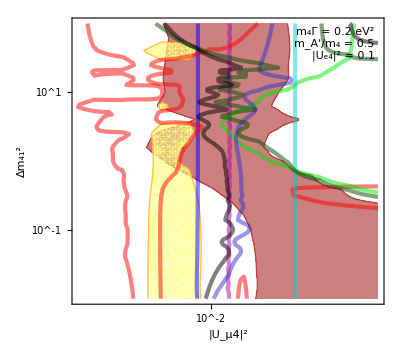
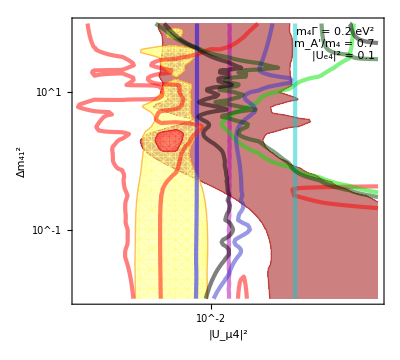
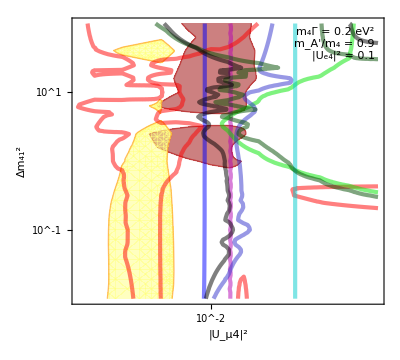
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Grid[Partition[Table[
Show[MyPlot["lsnd-ivan",Sequence@@key],MyPlot["mbjk",Sequence@@key],MyPlot["opera",Sequence@@key],MyPlot["icarus",Sequence@@key],MyPlot["app",Sequence@@key],MyPlot["app-proj"],
Sequence@@(MyPlot[#]&/@ExtKeys),PlotRange->{{-3.2,All},{-1.5,1.5}},
FrameLabel->{"|U_μ4|^2","Δm_41^2"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
Epilog->{
(*MyStyles⟦2,1,1⟧,Text["LSND",{-2,0.17},{-1,-1},{1,-.8}],
Black,Text["MiniBooNE",{-2.4,1.5},{-1,-1}],
MyStyles⟦3,1⟧,Text["OPERA",{-1.62,0.2},{-1,1},{0,1}],*)
Black,Text[Pane[Style[(*"99% C.L.\n"<>*)
"m_4Γ = "<>ToString[m4Γ[Prepend[key,"mbjk"]]]<>" eV^2\n"<>
"m_A'/m_4 = "<>ToString[mAm4[Prepend[key,"mbjk"]]]<>"\n"<>
"|U_e4|^2 = "<>ToString[thisUe4^2],TextAlignment->Right],FrameMargins->5],Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]
}],
{key,Union[RunList⟦;;-2,{2,3}⟧]}],UpTo[3]]]
```

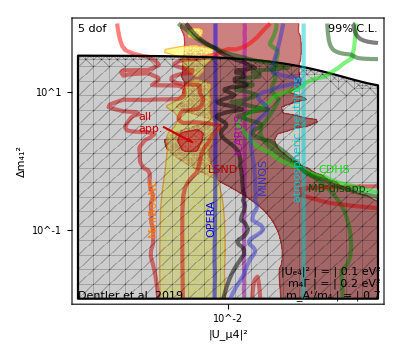

```mathematica
key={"0.2","0.7"};
MyLegend1=Framed[Grid[{
{"|U_e4|^2","=",ToString[thisUe4^2]<>" eV^2"},
{"m_4Γ","=",ToString[m4Γ[Prepend[key,"mbjk"]]]<>" eV^2"},
{"m_A'/m_4","=",ToString[mAm4[Prepend[key,"mbjk"]]]}
},Alignment->{{Right,Center,Left},{Baseline}},ItemSize->{Automatic,1.1},
Spacings->{{0.5,{0.2}},0.2}],Background->GrayLevel[1,.8]];
PerturbativityPlot=RegionPlot[m4G/(1-Ue4^2-Um4^2)/(Ue4^2+Um4^2)>0.25dm41(1-mϕm4^2)^2//.{Ue4->thisUe4,Um4->Sqrt[10^logUm4sq],dm41->10^logdm41,m4G->m4Γ[Prepend[key,"mbjk"]],mϕm4->mAm4[Prepend[key,"mbjk"]]},{logUm4sq,-3.5,-0.5},{logdm41,-2,2},BoundaryStyle->Directive[Black],PlotStyle->GrayLevel[0,.2]];
Show[MyPlot["lsnd-ivan",Sequence@@key],MyPlot["mbjk",Sequence@@key],MyPlot["opera",Sequence@@key],MyPlot["icarus",Sequence@@key],MyPlot["e776",Sequence@@key],MyPlot["app",Sequence@@key],MyPlot["app-proj"],PerturbativityPlot,
Sequence@@(MyPlot[#]&/@ExtKeys),PlotRange->{{-3,All},{-1.5,1.5}},
FrameLabel->{"|U_μ4|^2","Δm_41^2"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
Epilog->{
Inset[MyLegend1,Scaled[{0.99,0.01}],{1,-1}],
Black,Text["99% C.L.",Scaled[{0.98,0.98}],{1,1},Background->GrayLevel[1,.7]],
MyStyle["lsnd-ivan"]⟦1,1⟧,Text[Style["LSND",Background->MyStyle["lsnd-ivan"]⟦2,1⟧],{-2.2,-0.2},{-1,-1},{1,-0.6}],
MyStyle["mbjk"]⟦1,1⟧,Text["MiniBooNE",{-2.7,-1.1},{-1,-1},{0,1}],
MyStyle["opera"]⟦1⟧,Text["OPERA",{-2.12,-1.1},{-1,-1},{0,1}],
MyStyle["icarus"]⟦1⟧,Text[Style["ICARUS",Background->MyStyle["lsnd-ivan"]⟦2,1⟧],{-1.84,0.1},{-1,-1},{0,1}],
MyStyle["atm"]⟦1⟧,Text["atmospheric neutrinos",{-1.25,-0.6},{-1,-1},{0,1},Background->GrayLevel[1.,.8]],
MyStyle["mb200dis"]⟦1⟧,Text["MB disapp.",{-1.2,-0.48},{-1,-1},{1,-0.3}],
MyStyle["cdhs"]⟦1⟧,Text["CDHS",{-1.1,-0.2},{-1,-1},{1,-0.3}],
MyStyle["Minos"]⟦1⟧,Text["MINOS",{-1.7,-0.5},{-1,1},{0,1}],
MyStyle["app"]⟦1,1⟧,Text[Style["all\napp.",LineSpacing->{0.8,0}],{-2.9,0.4},{-1,-1}],
AbsoluteThickness[1.5],Arrow[{{-2.65,0.5},{-2.35,0.27}}],
Black,Text["5 dof",Scaled[{0.02,0.98}],{-1,1}],
Text["Dentler et al. 2019",Scaled[{0.02,0.01}],{-1,-1},Background->GrayLevel[1,.7]]
},PlotRangePadding->0]
```

#### Δm_41^2 vs. sin^2 2 θ_μe

```mathematica
ExpList={(*"lsnd-ivan",*)"mbjk","opera"};
M4GList={"1.0"};
MAM4List={"0.75"};
Clear[DataFiles,RunList,Chi2Min];
RunList=Flatten[Outer[List,ExpList,M4GList,MAM4List],2];
For[i=1,i≤Length[RunList],i++,
DataFiles[i]="8-oscdecay/dm41s22thmeUm4-"<>RunList⟦i,1⟧<>"-m4G"<>RunList⟦i,2⟧<>"-MAM4"<>RunList⟦i,3⟧<>".dat"];

For[i=1,i≤Length[RunList],i++,
key=RunList⟦i⟧;
DataRaw[i]=KPImport[DataFiles[i],"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[Sqrt[10^#⟦2⟧]/10^#⟦3⟧>1,1.*^12,#⟦4⟧]}&/@Data[i];
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i]=Select[#,#⟦3⟧==-1.7&]⟦1,{1,2,4}⟧&/@Data[i], (* select specific Subscript[U, μ4] *)
(*Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* select optimum Subscript[U, μ4] *)*)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
logs22thMin[i]=Min[Data[i]⟦All,2⟧];
logs22thMax[i]=Max[Data[i]⟦All,2⟧];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
m4Γ[i]=ExtractParam[BFP[i],"M4_GAMMA"];
mAm4[i]=ExtractParam[BFP[i],"MA_OVER_M4"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
m4Γ[i]=ExtractParam[Import[DataFiles[i],"Text"],"M4_GAMMA"];
mAm4[i]=ExtractParam[Import[DataFiles[i],"Text"],"MA_OVER_M4"]
]; (* End[if] *)
mAm4[key]=mAm4[i];
m4Γ[key]=m4Γ[i];
Chi2Min[key]=Chi2Min[i];
BFP[key]=BFP[i];

Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],logs22thMin[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no - osc)^2=",Chi2NoOsc[i],", Δχ_(no - osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

Best fit: sin^22θ_μe=0.0000977237, Δm^2=2.51189

χ_min^2=344.032, χ_(no - osc)^2=353.571, Δχ_(no - osc.)^2=9.53837 (CL 0.991513)

Best fit: sin^22θ_μe=0.000245471, Δm^2=10

χ_min^2=0.658141, χ_(no - osc)^2=0.688114, Δχ_(no - osc.)^2=0.0299724 (CL 0.0148744)

```mathematica
Clear[MyPlot];
For[i=1,i≤Length[RunList],i++,
If[Head[MyStyle[RunList⟦i,1⟧]⟦1⟧]===List,
MyPlot[Sequence@@RunList⟦i⟧]=ContourPlot[DataInterpol[i][logdm41,logs22thme]-Chi2Min[i],{logs22thme,logs22thMin[i],logs22thMax[i]},{logdm41,logdmsqMin[i],logdmsqMax[i]},PlotRange->Full,Contours->MyContours,ContourShading->MyStyle[RunList⟦i,1⟧]⟦2⟧,ContourStyle->MyStyle[RunList⟦i,1⟧]⟦1⟧,PlotPoints->100],
(* Else *)
MyPlot[Sequence@@RunList⟦i⟧]=ContourPlot[DataInterpol[i][logdm41,logs22thme]-Chi2Min[i],{logs22thme,logs22thMin[i],logs22thMax[i]},{logdm41,logdmsqMin[i],logdmsqMax[i]},PlotRange->Full,Contours->MyContours,ContourShading->False,ContourStyle->MyStyle[RunList⟦i,1⟧]]
]
];
```

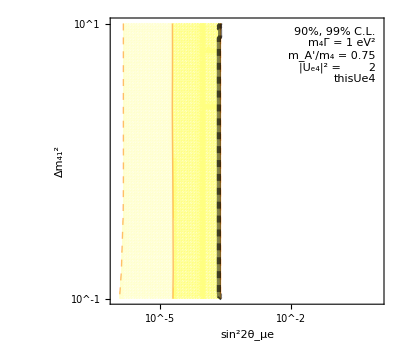

```mathematica
Grid[Table[
{Show[(*MyPlot["lsnd-ivan",Sequence@@key],*)MyPlot["mbjk",Sequence@@key],MyPlot["opera",Sequence@@key],
FrameLabel->{"sin^22θ_μe","Δm_41^2"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
Epilog->{
(*MyStyles⟦2,1,1⟧,Text["LSND",{-2,0.17},{-1,-1},{1,-.8}],
Black,Text["MiniBooNE",{-2.4,1.5},{-1,-1}],
MyStyles⟦3,1⟧,Text["OPERA",{-1.62,0.2},{-1,1},{0,1}],*)
Black,Text[Pane[Style["90%, 99% C.L.\n"<>
"m_4Γ = "<>ToString[m4Γ[Prepend[key,"mbjk"]]]<>" eV^2\n"<>
"m_A'/m_4 = "<>ToString[mAm4[Prepend[key,"mbjk"]]]<>"\n"<>
"|U_e4|^2 = "<>ToString[thisUe4^2],TextAlignment->Right],FrameMargins->5],Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]
}]},
{key,Union[RunList⟦All,{2,3}⟧]}]]
```

#### χ^2 vs. m_4 Γ

```mathematica
ExpList={"lsnd-ivan","mbjk","opera","icarus","e776"};
dm41List={"1","10","100"};
RunList=Flatten[Outer[List,ExpList,dm41List],1];
Clear[DataFiles];
For[i=1,i≤Length[RunList],i++,
DataFiles[i]="8-oscdecay/m4GUe4Um4-dm"<>RunList⟦i,2⟧<>"-"<>RunList⟦i,1⟧<>".dat"];

For[i=1,i≤Length[RunList],i++,
key=RunList⟦i⟧;
DataRaw[i]=KPImport[DataFiles[i],"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
Data[i]=Select[Data[i],#⟦3⟧≤0.1&]; (* enforce rough Subscript[U, μ4] constraint *)
Data[i]=Split[Sort[Data[i]],#1⟦1⟧==#2⟦1⟧&];
Data[i]={#⟦1,1⟧,Min[#⟦All,-1⟧]}&/@Data[i]; (* select optimum Subscript[U, e4] and Subscript[U, μ4] *)

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
m4ΓMin[i]=Min[Data[i]⟦All,1⟧];
m4ΓMax[i]=Max[Data[i]⟦All,1⟧];
dm41[key]=dm41[i]=ExtractParam[Import[DataFiles[i],"Text"],"DM41"];
]; (* End[loop over data files] *)
```

```mathematica
Clear[MyPlot];
For[i=1,i≤Length[RunList],i++,
If[Head[MyStyle[RunList⟦i,1⟧]⟦1⟧]===List,
MyPlot[Sequence@@RunList⟦i⟧]=Plot[DataInterpol[i][m4Γ]-Min[Data[i]⟦All,-1⟧],{m4Γ,m4ΓMin[i],m4ΓMax[i]},PlotStyle->MyStyle[RunList⟦i,1⟧]⟦1⟧],
(* Else *)
MyPlot[Sequence@@RunList⟦i⟧]=Plot[DataInterpol[i][m4Γ]-Min[Data[i]⟦All,-1⟧],{m4Γ,m4ΓMin[i],m4ΓMax[i]},PlotStyle->MyStyle[RunList⟦i,1⟧]]
]
];
```

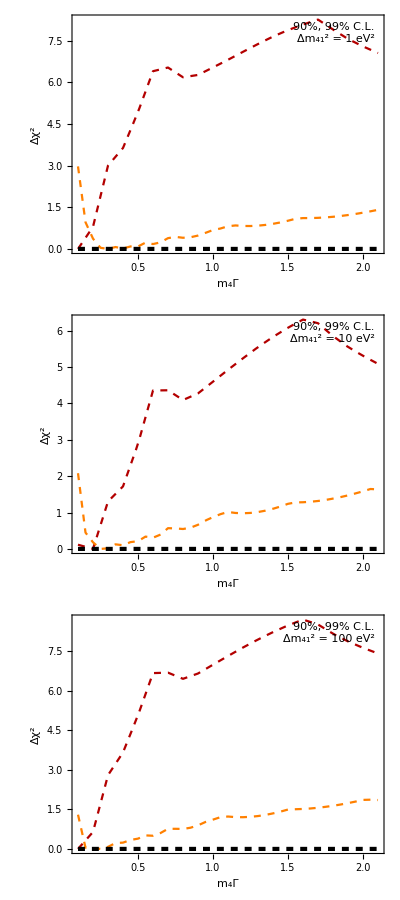

```mathematica
Grid[Table[
{Show[MyPlot["lsnd-ivan",Sequence@@key],MyPlot["mbjk",Sequence@@key],MyPlot["opera",Sequence@@key],
FrameLabel->{"m_4Γ","Δχ^2"},FrameTicks->Automatic,
Epilog->{
(*MyStyles⟦2,1,1⟧,Text["LSND",{-2,0.17},{-1,-1},{1,-.8}],
Black,Text["MiniBooNE",{-2.4,1.5},{-1,-1}],
MyStyles⟦3,1⟧,Text["OPERA",{-1.62,0.2},{-1,1},{0,1}],*)
Black,Text[Pane[Style["90%, 99% C.L.\n"<>
"Δm_41^2 = "<>ToString[dm41[{"mbjk",key}]]<>" eV^2\n",TextAlignment->Right],FrameMargins->5],Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]
}]},
{key,Union[RunList⟦All,2⟧]}]]
```